```mathematica
GoDown[n_] := Block[
{result={}, i=n},
While[i >1,
AppendTo[result,i];
i = If[OddQ[i],3 i +1, i /2]
];
AppendTo[result,1]
]
```

```mathematica
Table[
Length[GoDown[i]],{i,1,100}]
```

{1,2,8,3,6,9,17,4,20,7,15,10,10,18,18,5,13,21,21,8,8,16,16,11,24,11,112,19,19,19,107,6,27,14,14,22,22,22,35,9,110,9,30,17,17,17,105,12,25,25,25,12,12,113,113,20,33,20,33,20,20,108,108,7,28,28,28,15,15,15,103,23,116,23,15,23,23,36,36,10,23,111,111,10,10,31,31,18,31,18,93,18,18,106,106,13,119,26,26,26}

```mathematica
GoUp[n_] := Block[
{result={}, i=n},
If[i>4 && IntegerQ[(i-1)/3],AppendTo[result,(i-1)/3]];
AppendTo[result,i*2];
result
]
```

```mathematica
Experiment[max_]:=Module[
{i, j,Current, All={}, New,Result={}},
Current={1};
Monitor[
For[i=1,i≤max,i++,
All=Join[All,Current];
New={};
Monitor[
For[j=1, j ≤ Length[Current], j++,
New = Join[New, GoUp[Current[[j]]]]
],
j];
New = DeleteDuplicates[New];
Current ={};
For[j=1,j ≤ Length[New],j++,
If[!MemberQ[All, New[[j]]], AppendTo[Current, New[[j]]]]
];
Current=Sort[Current];
AppendTo[Result,Map[{i,#}&,Current]];
]
,i];
Flatten[Result,1]
]
```

```mathematica
a=Experiment[38]
```

{{1,2},{2,4},{3,8},{4,16},{5,5},{5,32},{6,10},{6,64},{7,3},{7,20},{7,21},{7,128},{8,6},{8,40},{8,42},{8,256},{9,12},{9,13},{9,80},{9,84},{9,85},{9,512},{10,24},{10,26},{10,28},{10,160},{10,168},{10,170},{10,1024},{11,9},{11,48},{11,52},{11,53},{11,56},{11,320},{11,336},{11,340},{11,341},{11,2048},{12,17},«44760»,{38,7635492864},{38,7635494912},{38,7635495424},{38,7635495552},{38,7635495584},{38,7635495592},{38,7635495594},{38,7635496960},{38,7635497216},{38,7635497280},{38,7635497296},{38,7635497300},{38,7635497301},{38,7635497344},{38,7635497376},{38,7635497384},{38,7635497386},{38,7635497408},{38,7635497412},{38,7635497413},{38,7635497414},{38,42949672960},{38,45097156608},{38,45634027520},{38,45768245248},{38,45801799680},{38,45810188288},{38,45812285440},{38,45812809728},{38,45812940800},{38,45812973568},{38,45812981760},{38,45812983808},{38,45812984320},{38,45812984448},{38,45812984480},{38,45812984488},{38,45812984490},{38,274877906944}}

```mathematica
Table[Map[Log[#[[2]]]&,Select[Take [a,-30],#[[1]]==i&] ],{i,1,35}]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{Log[954436864],Log[954436928],Log[954436944],Log[954436948],Log[954436949],Log[954437120],Log[954437152],Log[954437160],Log[954437162],Log[954437168],Log[954437172],Log[954437173],Log[954437176],Log[5368709120],Log[5637144576],Log[5704253440],Log[5721030656],Log[5725224960],Log[5726273536],Log[5726535680],Log[5726601216],Log[5726617600],Log[5726621696],Log[5726622720],Log[5726622976],Log[5726623040],Log[5726623056],Log[5726623060],Log[5726623061],Log[34359738368]}}

```mathematica
Select[Take [a,-30],#[[1]]==i&]
```

```mathematica
Table[Map[Log[#[[2]]]&,Select[a,#[[1]]==i&] ],{i,10,38}]
```

{{Log[24],Log[26],Log[28],Log[160],Log[168],Log[170],Log[1024]},{Log[9],Log[48],Log[52],Log[53],Log[56],Log[320],Log[336],Log[340],Log[341],Log[2048]},{Log[17],Log[18],Log[96],Log[104],Log[106],Log[112],Log[113],Log[640],Log[672],Log[680],Log[682],Log[4096]},{Log[34],Log[35],Log[36],Log[37],Log[192],Log[208],Log[212],Log[213],Log[224],Log[226],Log[227],Log[1280],Log[1344],Log[1360],Log[1364],Log[1365],Log[8192]},«22»,{},{},{}}

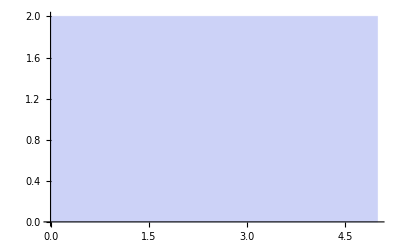
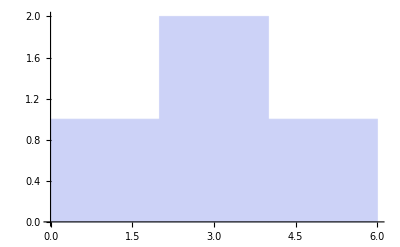
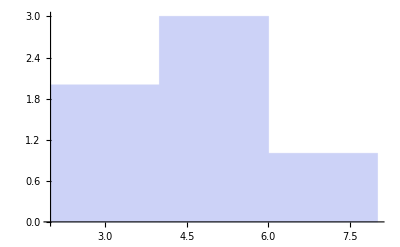
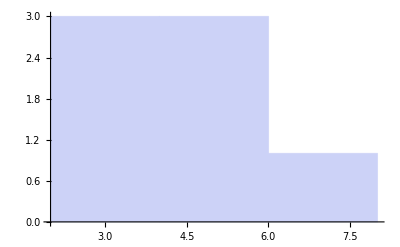
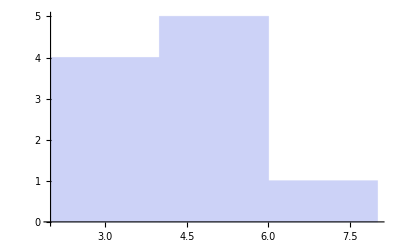
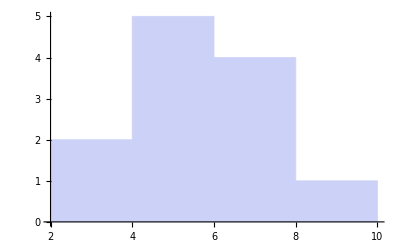
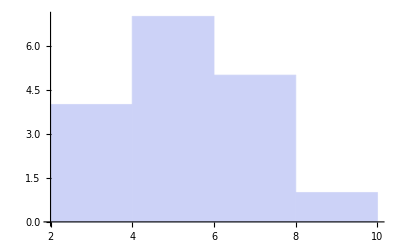
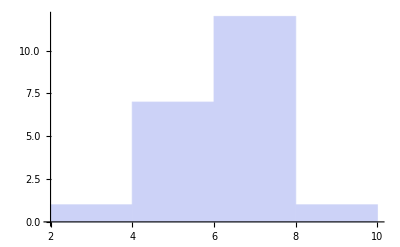
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
Histogram[
Map[N[Log[#[[2]]]]&,Select[a,#[[1]]==i&] ]
],{i,5,38}
]
```

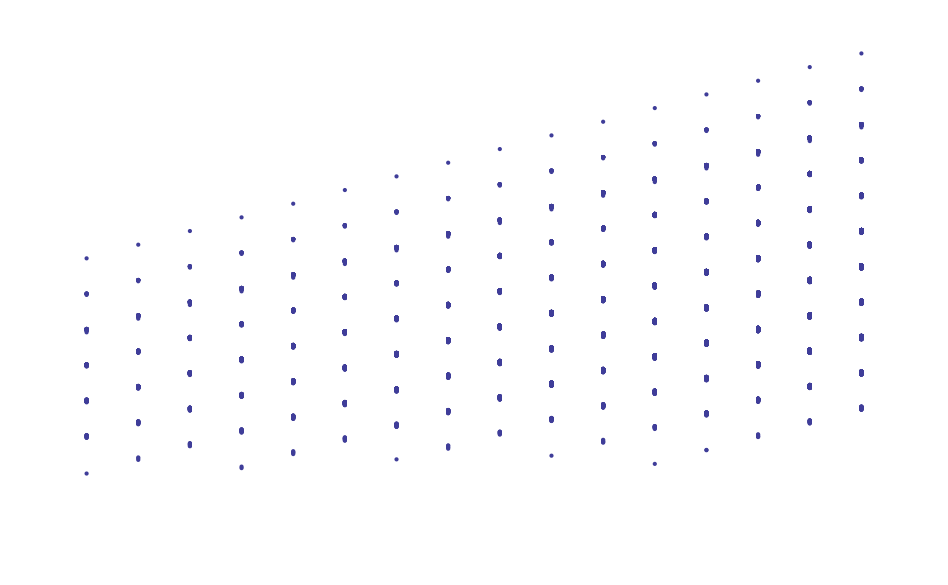

```mathematica
ListLogPlot[Experiment[35],Axes->False]
```

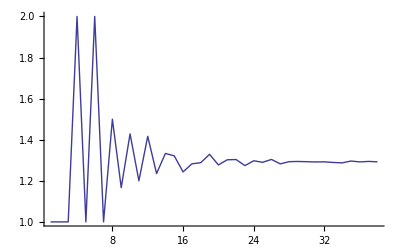

```mathematica
ListPlot[Ratios[Map[Length[#]&,Experiment[39]]],Joined->True]
```

```mathematica
RSolve[{a[n+1]==1.3 * a[n],a[0]==1},a[n],n]
```

{{a[n]→1. 1.3^n}}

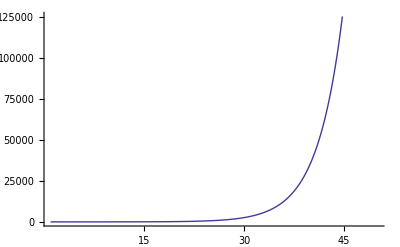

```mathematica
Plot[1.3^n,{n,1,50}]
```

```mathematica
Numerator[Ratios[Map[Length[#]&,Experiment[35]]]]
```

{1,1,1,2,1,2,1,3,7,10,6,17,21,4,37,46,59,76,101,129,56,73,93,362,467,609,781,1010,1307,1690,2183,2821,3637,4682}

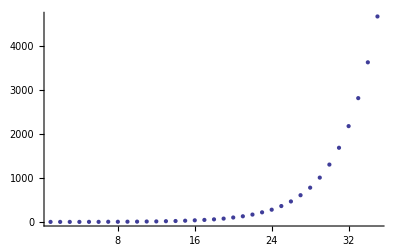

```mathematica
ListPlot[Map[Length[#]&,Experiment[35]]]
```

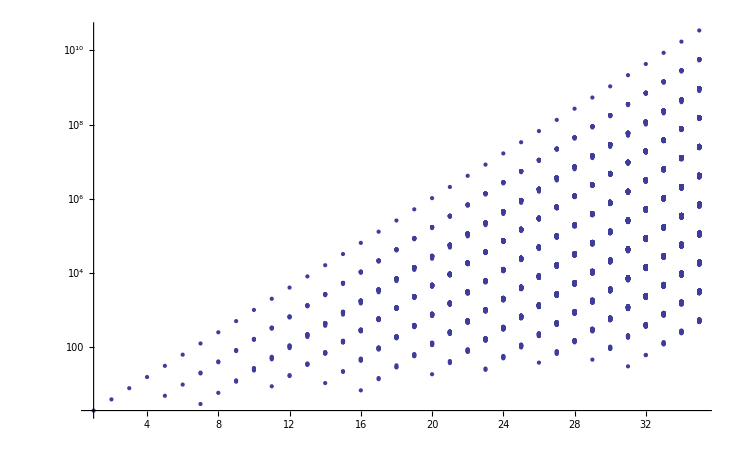

```mathematica
ListLogPlot[Experiment[35],Axes->True, PlotRange->All]
```

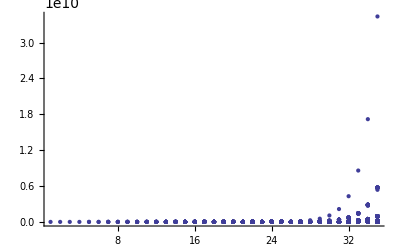

```mathematica
ListPlot[Experiment[35],Axes->True, PlotRange->All]
```